```mathematica
(*Quit[];*)
```

```mathematica
Get["Replacements`"];
PStyle={{Red,Thick}, {Blue,Dashed}};
```

## ReplComplexLog

Real part:

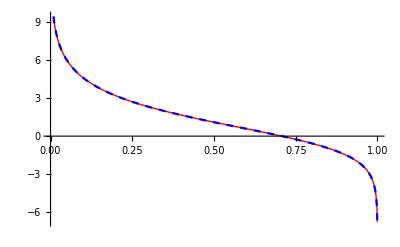

```mathematica
Plot[{Re[Log[1-1/xs^2]],Re[Log[1-1/xs^2]/.ReplComplexLog/.cI-> I]},{xs,0,1},PlotStyle->PStyle]
```

Imaginary part:

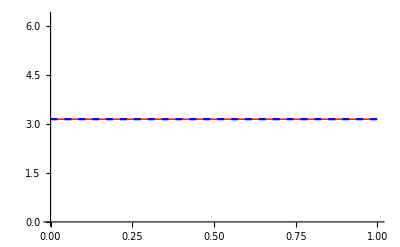

```mathematica
Plot[{Im[Log[1-1/xs^2]],Im[Log[1-1/xs^2]/.ReplComplexLog/.cI-> I]},{xs,0,1},PlotStyle->PStyle]
```

```mathematica
Plot[{Im[Log[1-1/xs^2]],π},{xs,0,1},PlotStyle->PStyle]
```

-Graphics-

## ReplComplexPolyLog2

Real part:

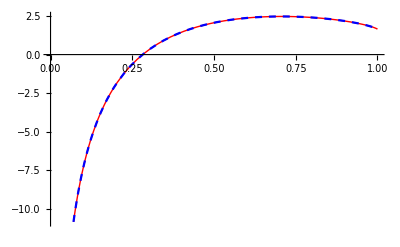

```mathematica
Plot[{Re[PolyLog[2,1/xs^2]],Re[PolyLog[2,1/xs^2]/.ReplComplexPolyLog2/.cI-> I]},{xs,0,1},PlotStyle->PStyle]
```

Imaginary part:

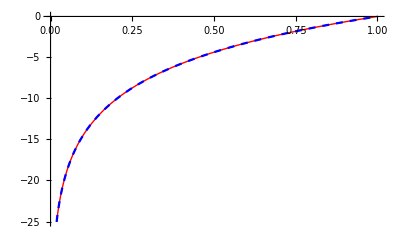

```mathematica
Plot[{Im[PolyLog[2,1/xs^2]],Im[PolyLog[2,1/xs^2]/.ReplComplexPolyLog2/.cI-> I]},{xs,0,1},PlotStyle->PStyle]
```

```mathematica
Plot[{Im[PolyLog[2,1/xs^2]],2π Log[xs]},{xs,0,1},PlotStyle->PStyle]
```

-Graphics-

## ReplComplexPolyLog3

Real part:

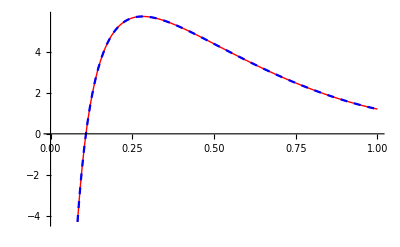

```mathematica
Plot[{Re[PolyLog[3,1/xs^2]],Re[PolyLog[3,1/xs^2]/.ReplComplexPolyLog3/.cI-> I]},{xs,0,1},PlotStyle->PStyle]
```

Imaginary part:

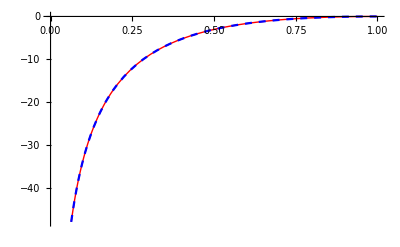

```mathematica
Plot[{Im[PolyLog[3,1/xs^2]],Im[PolyLog[3,1/xs^2]/.ReplComplexPolyLog3/.cI-> I]},{xs,0,1},PlotStyle->PStyle]
```

```mathematica
Plot[{Im[PolyLog[3,1/xs^2]],-2π Log[xs]^2},{xs,0,1},PlotStyle->PStyle]
```

-Graphics-